```mathematica
(* Basic Operation *)
a=2;
b=3;
a+b
a-b
a*b
a/b
a^b
a!
b!
ClearAll["Global`*"]
```

5

-1

6

2/3

8

2

6

```mathematica
(* Trigonometry *)
Sin[π/3]
Cos[π/3]
Tan[π/3]
```

(√3)/2

1/2

√3

```mathematica
(* Complex *)
1+2I
3Exp[2I]
Abs[3Exp[2I]]
```

1+2 ⅈ

3 ⅇ^(2 ⅈ)

3

```mathematica
(* Symbolic Algebra and Manipulation *)
Expand[(x+3)(x+2)]
Factor[1+2x+x^2]
FullSimplify[x Gamma[x]]
```

6+5 x+x^2

(1+x)^2

Gamma[1+x]

```mathematica
(* Summation *)
Sum[x^2,x]
Sum[x^2,{x,1,n}]
Sum[x^2,{x,10}]
```

1/6 (-1+x) x (-1+2 x)

1/6 n (1+n) (1+2 n)

385

```mathematica
(* Product *)
Product[i^2,{i,1,n}]
Product[i^2,{i,1,5}]
```

(n!)^2

14400

```mathematica
(* Limit *)
Limit[Sin[x]/x,x->0]
Limit[(1+Sinh[x])/Exp[x],x->∞]
```

1

1/2

```mathematica
(* Differentiation *)
D[x^n,x]
D[Cos[x],{x,n}]
D[Sin[x y]/(x^2+y^2),x,y]
```

n x^(-1+n)

Cos[(n π)/2+x]

-(2 x^2 Cos[x y])/((x^2+y^2)^2)-(2 y^2 Cos[x y])/((x^2+y^2)^2)+Cos[x y]/(x^2+y^2)+(8 x y Sin[x y])/((x^2+y^2)^3)-(x y Sin[x y])/(x^2+y^2)

```mathematica
(* Integration *)
Integrate[1/x,x]
Integrate[x^n+Sin[x],x]
Integrate[Exp[-x^2],x]
```

Log[x]

x^(1+n)/(1+n)-Cos[x]

1/2 √π Erf[x]

```mathematica
(* Equation Solving *)
Solve[a x^2+b x+c==0,x]
FindRoot[Exp[-x^2]Cos[x],{x,1}]
FindRoot[Cos[x]==x,{x,1}]
DSolve[f'[x]==f[x],f[x],x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

{x→1.5708}

{x→0.739085}

{{f[x]→ⅇ^x C[1]}}

```mathematica
(* Linear Algebra *)
{a,b,c} .{x,y,z}
Dot[{a,b,c} ,{x,y,z}]
Transpose[{{a,b,c},{x,y,z}}]//MatrixForm
Inverse[{{x,y},{y,x}}]//MatrixForm
Det[{{a,b},{c,d}}]
LinearSolve[{{a,b},{c,d}},{x,y}]//MatrixForm
Eigenvalues[{{1,2,3},{4,5,6},{7,8,9}}]//MatrixForm
```

a x+b y+c z

a x+b y+c z

(a | x
b | y
c | z)

(x/(x^2-y^2) | -y/(x^2-y^2)
-y/(x^2-y^2) | x/(x^2-y^2))

-b c+a d

((d x-b y)/(-b c+a d)
(c x-a y)/(b c-a d))

(3/2 (5+√33)
3/2 (5-√33)
0)

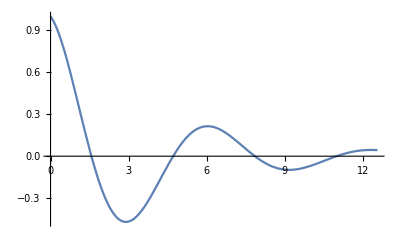

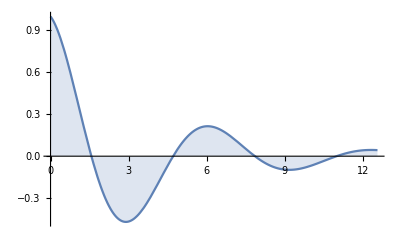

-Graphics-

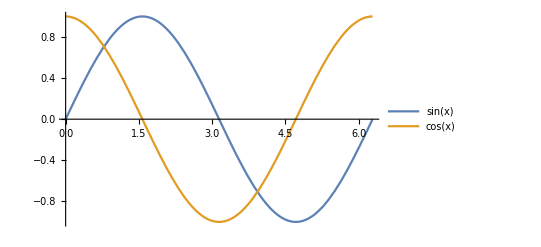

```mathematica
(* Graphics 2D *)
Plot[Exp[-x/2^2]Cos[x],{x,0,4Pi}]
Plot[Exp[-x/2^2]Cos[x],{x,0,4Pi},Filling->Axis]
Plot[{Sin[x],Cos[x]},{x,0,2Pi},PlotLabels->"Expressions"]
Plot[{Sin[x],Cos[x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

```mathematica
(* Graphics 3D *)
Plot3D[Sin[x+y^2],{x,-3,3},{y,-3,3},PlotPoints->100,ColorFunction->"DeepSeaColors"]
Plot3D[{x^2+y^2,-x^2-y^2},{x,-5,5},{y,-5,5},ColorFunction->"RustTones"]
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

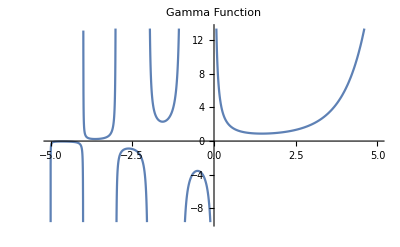

-Graphics3D-

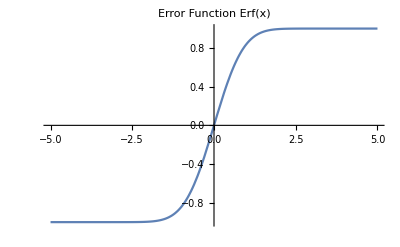

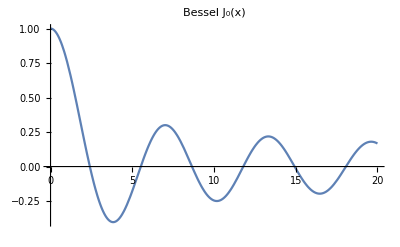

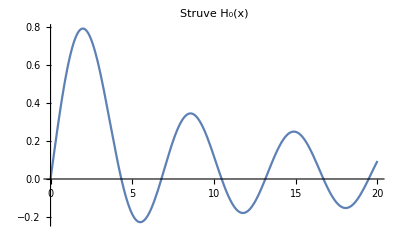

```mathematica
(* Special Function *)
Plot[Gamma[z],{z,-5,5},PlotLabel->"Gamma Function"]
Plot3D[Beta[x,y],{x,0.1,5},{y,0.1,5},PlotPoints->100,ColorFunction->"DeepSeaColors",PlotLabel->"Beta Function"]
Plot[Erf[x],{x,-5,5},PlotLabel->"Error Function Erf(x)"]
Plot[BesselJ[0,x],{x,0,20},PlotLabel->"Bessel J₀(x)"]
Plot[StruveH[0,x],{x,0,20},PlotLabel->"Struve H₀(x)"]
```

1-1/2 (x-π/2)^2+1/24 (x-π/2)^4+O[x-π/2]^5

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

(1+x/2+x^2/9+x^3/72+x^4/1008+x^5/30240)/(1-x/2+x^2/9-x^3/72+x^4/1008-x^5/30240)

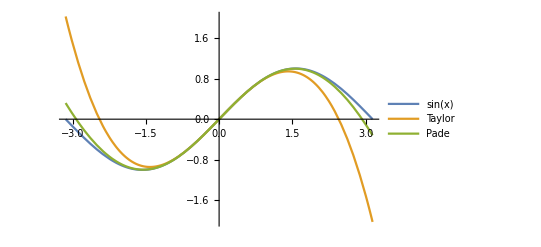

```mathematica
(* Series of Function *)
Series[Sin[x],{x,Pi/2,4}]
Series[Exp[x],{x,0,5}]
PadeApproximant[Exp[x],{x,0,5}]

f[x_]:=Sin[x];
taylor=Normal[Series[f[x],{x,0,3}]];
pade=PadeApproximant[f[x],{x,0,3}];
Plot[{f[x],taylor,pade},{x,-Pi,Pi},PlotLegends->{"sin(x)","Taylor","Pade"}]
```